```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"UTILITY_readBeamFiles.nb"}]]
```

```mathematica
POff = readBeamFile["~/POff.h5"];
PPlus = readBeamFile["~/PPlus.h5"];
PMinus = readBeamFile["~/PMinus.h5"];
```

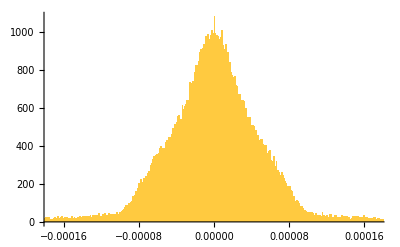

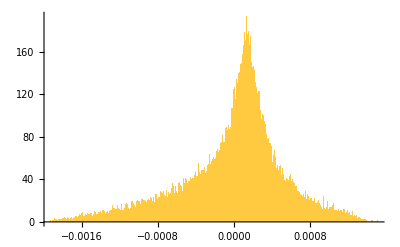

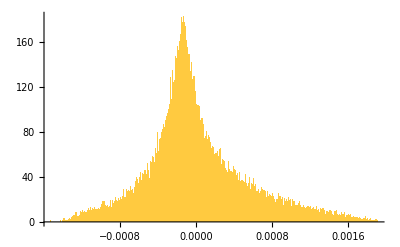

```mathematica
Histogram[POff[[All,"y"]],{1*^-6}]
Histogram[PPlus[[All,"y"]],{1*^-6}]
Histogram[PMinus[[All,"y"]],{1*^-6}]
```

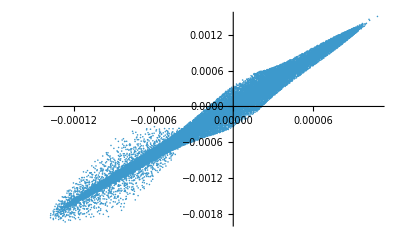

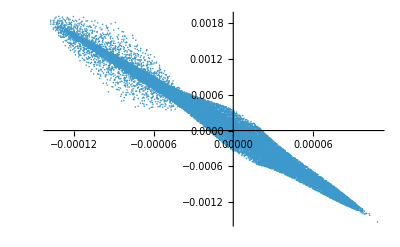

```mathematica
ListPlot[{#z,#y}&/@PPlus]
ListPlot[{#z,#y}&/@PMinus]
```

```mathematica
binMin = -0.002;
binMax = 0.002;
binStep = 10*^-6;
bins = MovingAverage[Table[x0,{x0,binMin,binMax,binStep}],2];

POffYData=BinCounts[POff[[All,"y"]],{binMin,binMax,binStep}];
POffYData = Transpose[{bins,POffYData}];

PPlusYData=BinCounts[PPlus[[All,"y"]],{binMin,binMax,binStep}];
PPlusYData = Transpose[{bins,PPlusYData}];
```

```mathematica
expr = A * Exp[(-(x-x0)^2)/(2 σ^2)];
nlmOff = NonlinearModelFit[
POffYData,
expr,
{
{A,10000},
{x0,0.0002},
{σ,0.0002}
},
x
]
```

FittedModel[…]

```mathematica
nlmOff["ParameterEstimates"]
```

General::munfl: Exp[-1139.01] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1127.62] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1116.28] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1144.63] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

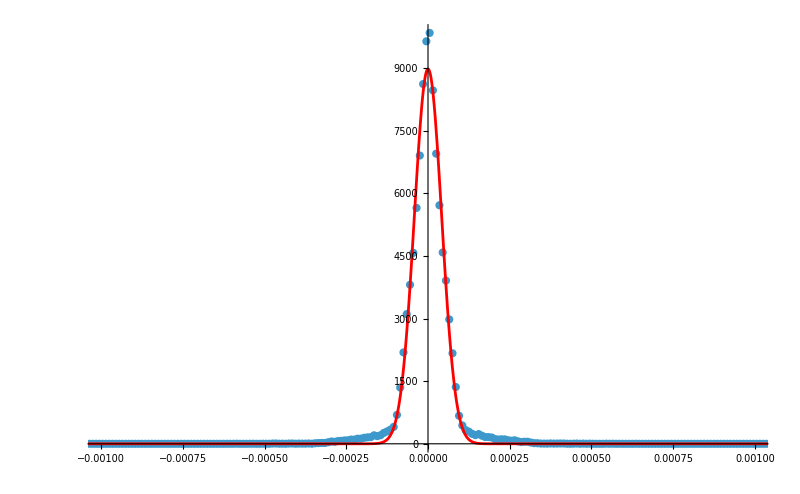

```mathematica
Show[
ListPlot[POffYData,PlotRange->{{-0.001,0.001},All},ImageSize->800],
Plot[nlmOff["BestFit"],{x,-0.002,0.002},PlotRange->All,PlotStyle->Red]

]
```

```mathematica
nlmPlus = NonlinearModelFit[
PPlusYData,
expr,
{
{A,2000},
{x0,0.0002},
{σ,0.0002}
},
x
];
```

```mathematica
nlmPlus["ParameterEstimates"]
```

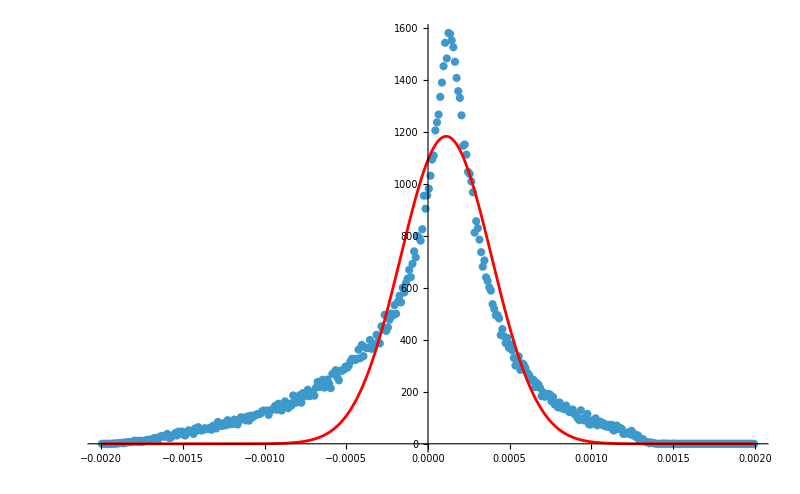

```mathematica
Show[
ListPlot[PPlusYData,PlotRange->{{-0.002,0.002},All},ImageSize->800],
Plot[nlmPlus["BestFit"],{x,-0.002,0.002},PlotRange->All,PlotStyle->Red]
]
```